# Coulomb Scattering

```mathematica
amu=931.5;
ℏ=197.3269788; (* MeV fm *)
ee=ℏ/137; (* e^2  in term of MeV fm *) 
mp=938.272;
mn=939.567;
d[Z1_,Z2_,Elab_,θlab_]:=(Z1 Z2 1.44)/(Elab(1-Tan[π/4-θlab/4]^2))
b[Z1_,Z2_,Elab_,θlab_]:=d[Z1,Z2,Elab,θlab]Tan[π/4-θlab/4]; 
MEcm[A1_,A2_,T1Lab_]:=Module[
{P1,P2,Pc,β,γ,L,P1c,P2c,mμ},
P1={A1 amu+T1Lab,√((A1 amu+T1Lab)^2-(A1 amu)^2)};
P2={A2 amu,0};
Pc = (P1+P2)/2;
β=Pc[[2]]/Pc[[1]];
γ=1/(√(1-β^2));
L=γ{{1,-β},{-β,1}};
P1c=L.P1;
P2c=L.P2;
(*Print[Simplify[P1c[[1]]-A1 amu,m1+m2+T>0]];*)
(*{mμ=(A1 A2)/(A1+A2),P1c[[1]]-A1 amu }*)
{mμ=(P1c[[1]]P2c[[1]])/(P1[[1]]+P2[[1]]),1/(2mμ)((P1c[[1]])^2-(A1 amu)^2)}

]
SphericalBesselH[l_,k_,r_,sign_]:=k r SphericalBesselJ[l, k r]-sign k r SphericalBesselY[l,k r](*the minus sign is needed*) 
(*FL[L_,η_,ρ_]:=(2^L Exp[-π η/2]Abs[Gamma[L+1+ⅈ η]])/Gamma[2L+2] ρ^(L+1)Exp[-ⅈ ρ]Hypergeometric1F1[L+1-ⅈ η,2L+2,2 ⅈ ρ];*)
CoulombPS[L_,η_]:=Arg[Gamma[1+L+ⅈ η]];
HL[L_,η_,ρ_,sign_]:=Exp[sign ⅈ (ρ-L π/2+CoulombPS[L,η]-η Log[2 ρ])]((-sign)2 ⅈ ρ)^(1+L + ⅈ η)HypergeometricU[1+L+sign ⅈ η,2L+2,-sign 2ⅈ ρ]
FL[L_,η_,ρ_]:=Im[HL[L,η,ρ,1]]
GL[L_,η_,ρ_]:=Re[HL[L,η,ρ,1]]
eta[Z1_,Z2_,E_,mμ_]:= (Z1 Z2 ee)/ℏ √(mμ/(2 E)); 
σRuth[θ_,Z1_,Z2_,E_]:=((Z1 Z2 ee)/(4 E))^2 10/Sin[θ/2]^4; (* 1 fm^2 = 10 mb *)
```

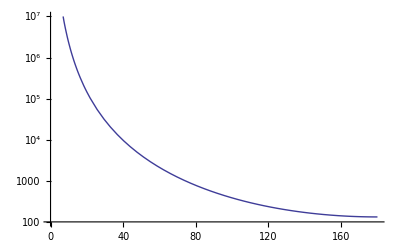

```mathematica
LogPlot[σRuth[θ Degree, 8, 82, 130/2],{θ,0,180},PlotRange->{10^2,10^7}]
```

```mathematica
Manipulate[
Plot[{
d[2,82,e,θ Degree],
b[2,82,e,θ Degree]
},{e,10,40}, GridLines->Automatic,
GridLinesStyle->Directive[Gray,Dashed],
 PlotLabel->Style["α+^208Pb elastic scattering at "<>ToString[θ]<>"^o",20],
PlotRange->{0,All},
PlotStyle->{Directive[Red,Thick],Directive[Blue,Thick]},
Epilog->{
Text[Style["Closet Dist.",Red,20],{30, d[2,82,30,60 Degree]+10}],
Text[Style["Impact Para.",Blue,20],{30, b[2,82,30,60 Degree]+10}]
},
Frame->True,FrameLabel->{Style["E_Lab [MeV]",20],Style["Distance [fm]",20]},
ImageSize->400,
AspectRatio->1.2
],
{{θ,60},10,180,10}]
```

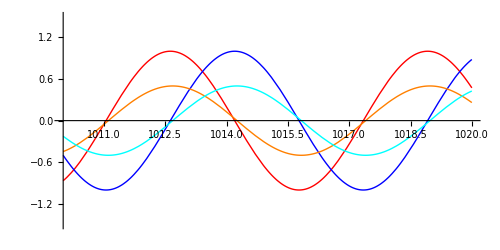

```mathematica
LLL=10;
ηηη=2;
Plot[{
Re[HL[LLL,ηηη,r,1]],
Im[HL[LLL,ηηη,r,1]],
0.5Cos[r-LLL π/2+CoulombPS[LLL,ηηη]-ηηη Log[2 r]],
0.5Sin[r-LLL π/2+CoulombPS[LLL,ηηη]-ηηη Log[2 r]]
}
,{r,1010,1020},PlotRange->{-1.5,1.5},PlotStyle->{Red,Blue,Orange,Cyan},ImageSize->500,AspectRatio->0.5]
```

```mathematica
RK4SE[U_Symbol,m_,T_,l_,v0_,rStart_,nStep_,h_,plotFlag_,verb_]:=Module[
{G,k,kv,kx,rEnd,SolU,SolR,η,dx,dv,g1,g2,norFac,maxU,maxF,maxR,βl,δl,n,R,ρ,L1,jl,jlD,nl,nlD,maxH,func,SSR,signSSR},
k=√((2 m T)/ℏ^2);
η=eta[1,1,m,T];
G[r_,u_,v_]:=(2m)/ℏ^2(U[r]-T)u+(l(l+1))/r^2 u;
kv={0,0,0,0};
kx={0,0,0,0};
rEnd=rStart + h nStep;
SolU=Table[{ρ,0,0},{ρ,rStart,rEnd,h}];
SolU[[1,2]]=0; (* u[0] = 0  for convergence *)
SolU[[1,3]]=v0;
If[verb>1,Print[{"k",k,"λ",(2π)/k,"step",h,"nStep+1",nStep+1,"η",η}]];
Monitor[Table[
kv[[1]]=G[SolU[[i,1]],SolU[[i,2]],SolU[[i,3]]];
kx[[1]]=SolU[[i,3]];
kv[[2]]=G[SolU[[i,1]]+h/2,SolU[[i,2]]+kx[[1]] h/2, SolU[[i,3]]+kv[[1]] h/2];
kx[[2]]=SolU[[i,3]]+kv[[1]] h/2;
kv[[3]]=G[SolU[[i,1]]+h/2,SolU[[i,2]]+kx[[2]] h/2, SolU[[i,3]]+kv[[2]] h/2];
kx[[3]]=SolU[[i,3]]+kv[[2]] h/2;
kv[[4]]=G[SolU[[i,1]]+h,SolU[[i,2]]+kx[[3]] h, SolU[[i,3]]+kv[[3]] h];
kx[[4]]=SolU[[i,3]]+kv[[3]]h;
dx=h/6(kx[[1]]+2kx[[2]]+2kx[[3]]+kx[[4]]);
dv=h/6(kv[[1]]+2kv[[2]]+2kv[[3]]+kv[[4]]);
SolU[[i+1,3]]=SolU[[i,3]]+dv;
SolU[[i+1,2]]=SolU[[i,2]]+dx;
(*Print[{k,dx,SolU[[i]]}];*)
,{i,1,nStep}],i];
maxU=Max[SolU[[1;;-1,2]]];
maxF=1;(*FL[l,η,k SolU[[nStep-60,1]]];*)
norFac=maxF/maxU;
Print[{SolU[[nStep-60,1]],"Max u_l",maxU,"Max FL",maxF,"norm",norFac}];
SolU=Table[{SolU[[i,1]],norFac SolU[[i,2]],norFac SolU[[i,3]]},{i,1,nStep+1}];
SolR=Table[{SolU[[i,1]],SolU[[i,2]]/SolU[[i,1]],SolU[[i,3]]/SolU[[i,1]]-SolU[[i,2]]/SolU[[i,1]]^2},{i,nStep+1}];
maxR=Max[SolR[[1;;-1,2]]];
If[plotFlag==1,
g1=ListPlot[
Table[SolR[[i,1;;2]],{i,1,Length[SolU]}]
,Joined->True,PlotMarkers->Automatic,Frame->True,FrameLabel->{Style["r [fm]",18],Style["R_l",18]},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],PlotRange->1.1{-maxR,maxR}];
g2=Plot[{0.001(U[r]+ℏ^2/(2m)(l(l+1))/r^2),0.01T},{r,rStart,rEnd},PlotStyle->{Red,Green},PlotRange->All];
Print[Show[{g1,g2},ImageSize->600]];
];

(*maxU=Max[SolU[[-Floor[nStep/4];;-1,2]]];
n=Flatten[Position[SolU[[1;;-1,2]],maxU]][[1]];
R=SolU[[n,1]];
ρ=k R;
L1= SolU[[n,3]]/SolU[[n,2]];
jl=ρ SphericalBesselJ[l,ρ];
jlD=Evaluate[D[ k r SphericalBesselJ[l,k r],r]]/.{r->R};
nl=ρ SphericalBesselY[l,ρ];
nlD=Evaluate[D[- k r SphericalBesselY[l,k r],r]]/.{r->R};
βl= -(jlD-jl L1)/(nlD-nl L1);
δl=ArcTan[βl];
If[plotFlag==1,
maxH=MaxValue[{SphericalBesselH[l,k,r,βl],r>R},r];
SSR=Sum[(maxU/maxH SphericalBesselH[l,k,SolU[[i,1]],βl]-SolU[[i,2]])^2,{i,n,nStep+1}];
signSSR=Sign[10-SSR];
If[SSR>10,
SSR=Sum[(-maxU/maxHSphericalBesselH[l,k,SolU[[i,1]],βl]-SolU[[i,2]])^2,{i,n,nStep+1}];];
Print[
ListPlot[{
Table[{SolU[[i,1]],SolU[[i,2]]},{i,1,nStep+1}],
Table[{SolU[[i,1]],signSSR maxU/maxH SphericalBesselH[l,k,SolU[[i,1]],βl]},{i,1,nStep+1}]
},Joined->True,Frame->True,FrameLabel->{Style["r [fm]",18],Style["U_l",18]},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]
]
];
Print[{"SSR",SSR,"sign",signSSR}];
];*)
If[verb>0,Print[{"n",n,"R",R,"βl",βl,"δ [rad]",δl,"δ/π",δl 1/π}]];

{SolR,SolU,{k,δl,βl}}
]
```

```mathematica
Manipulate[Plot[CoulombPS[LLL,η] 1/π,{η,0,4}],{LLL,0,10,1}]
```

```mathematica
Manipulate[Plot[CoulombPS[LLL,eta[1,9, mp,Energy]] 1/π,{Energy,0.1,500}],{LLL,0,10,1}]
```

-0.000307566

{k,0.694213,λ,9.0508,step,0.1,nStep+1,701,η,0.000532844}

{63.901,Max u_l,1.58059,Max FL,1,norm,0.632677}

{n,n$4540,R,R$4540,βl,βl$4540,δ [rad],δl$4540,δ/π,δl$4540/π}

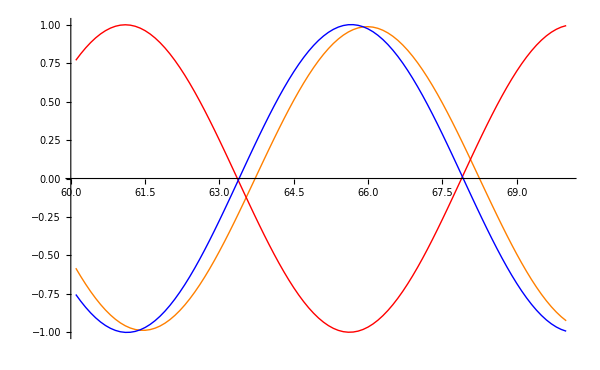

```mathematica
Pot[r_]:=ee/r;
LLL=0;
Energy=10;
eta[1,mp,Energy];
CoulombPS[LLL,eta[1,mp,Energy]]
ul=RK4SE[Pot,mp,Energy,LLL,1,0.001,700,0.1,0,2][[2]];
FLlist=Table[{ul[[i,1]], FL[LLL, eta[1,mp,Energy],(√(2 mp Energy))/ℏ ul[[i,1]]]},{i,1,Length[ul]}];
HLlist=Table[{ul[[i,1]], 
Re[1/(2ⅈ)(HL[LLL, eta[1,mp,Energy],(√(2 mp Energy))/ℏ ul[[i,1]],-1]-HL[LLL, eta[1,mp,Energy],(√(2 mp Energy))/ℏ ul[[i,1]],1])]},{i,1,Length[ul]}];
(*SHLlist=Table[{ul[[i,1]], 
0.001Re[i/2(SphericalBesselH[LLL,(√(2 mp Energy))/ℏ,ul[[i,1]],-1]-Exp[2ⅈ CoulombPS[LLL,eta[1,Energy,mp]]]SphericalBesselH[LLL,(√(2 mp Energy))/ℏ,ul[[i,1]],1])]},{i,1,Length[ul]}];*)
SHLlist=Table[{ul[[i,1]], 
SphericalBesselH[LLL,(√(2 mp Energy))/ℏ,ul[[i,1]],Tan[CoulombPS[LLL,eta[1,Energy,mp]]]]},{i,1,Length[ul]}];
Show[
ListPlot[{
ul[[-100;;-1,{1,2}]],
HLlist[[-100;;-1]],
SHLlist[[-100;;-1]]
},PlotStyle->{Orange,Red,Blue},Joined->True]
]
```

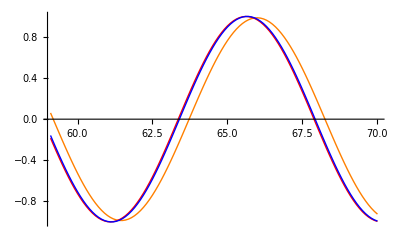

```mathematica
Show[
ListPlot[{
ul[[-110;;-1,{1,2}]],
FLlist[[-110;;-1]],
SHLlist[[-110;;-1]]
},PlotStyle->{Orange,Red,Blue},Joined->True]
]
```

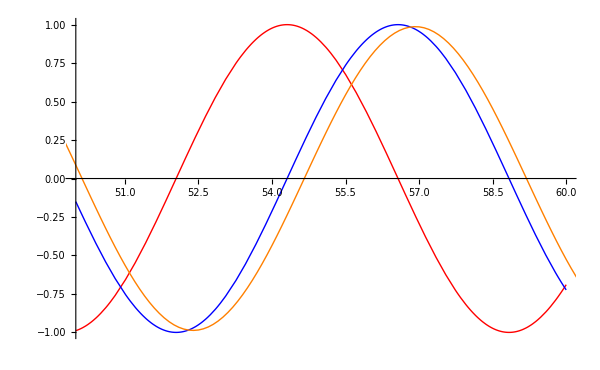

```mathematica
Show[
Plot[{
Cos[(√(2 mp Energy))/ℏ r-LLL π/2+CoulombPS[LLL,eta[1,mp,Energy]]-eta[1,mp,Energy] Log[2 (√(2 mp Energy))/ℏ r]],
Sin[(√(2 mp Energy))/ℏ r-LLL π/2+CoulombPS[LLL,eta[1,mp,Energy]]-eta[1,mp,Energy] Log[2 (√(2 mp Energy))/ℏ r]],
},{r,50,60},ImageSize->600,PlotStyle-> {Red,Blue,Darker[Green]}],
ListPlot[ul[[1;;-1,{1,2}]],PlotStyle->Orange,Joined->True]
]
```